Polinomio de Weierstrass que define a X_0(15)

```mathematica
f[x_,y_]:=y^2+x y+y-x^3-x^2+10x+10
```

Cambio de variable que simplifica la ecuación de Weierstrass:

```mathematica
coord[{x_,y_}]:={(x-15)/36,y/216-x/72-21/72}
```

La ecuación se transforma a

```mathematica
Simplify[f[(x-15)/36,y/216-x/72-21/72]]
```

(263466+12987 x-x^3+y^2)/46656

Define F como la ecuación de Weierstrass simplificada

```mathematica
F[x_,y_]:=y^2-x^3+12987 x+263466
```

Tres valores posibles para x para puntos de X_0(15) de la forma (x,0)

```mathematica
Solve[F[x,0]==0]
```

{{x→-102},{x→-21},{x→123}}

Para calcular el rango usamos el cambio de variable:

```mathematica
Simplify[F[x-21,y]]
```

11664 x+63 x^2-x^3+y^2

Para aplicar Lutz-Nagell, definimos la constante D como

```mathematica
d=4(-12987)^3+27(-263466)^2
```

-6887475360000

Su factorización en primos es:

```mathematica
CenterDot@@(Superscript@@@FactorInteger[d])
```

(-1)^1·2^8·3^16·5^4

El conjunto de divisores, positivos y negativos, cuyos cuadrados dividen el discriminante es

```mathematica
Divi=Union[Divisors[√-d],-Divisors[√-d]];
```

Vemos que divisores y_0, positivo o negativo, de √-d producen cúbicas de la forma F(x,y_0). Definimos “DiviB” como los divisores de √-d tales que la cúbica asociada tiene soluciones racionales x.

```mathematica
DiviB=Select[Divi,Length[Solve[F[x,#]==0,x,Integers]]>0&]
```

{-4860,-540,540,4860}

Producimos la tabla de las soluciones a las cúbicas asociadas a los divisores “buenos”:

```mathematica
Table[{Solve[F[x,y]==0,x,Integers],y},{y,DiviB}]
```

{{{{x→303}},-4860},{{{x→-57}},-540},{{{x→-57}},540},{{{x→303}},4860}}

Por lo tanto el grupo de puntos racionales (distintos de O ) de la ecuación F es

```mathematica
G={{-102,0},{-21,0},{123,0},{303,-4860},{303,4860},{-57,-540},{-57,540}};
```

Graficamos la curva elíptica junto con los puntos racionales:

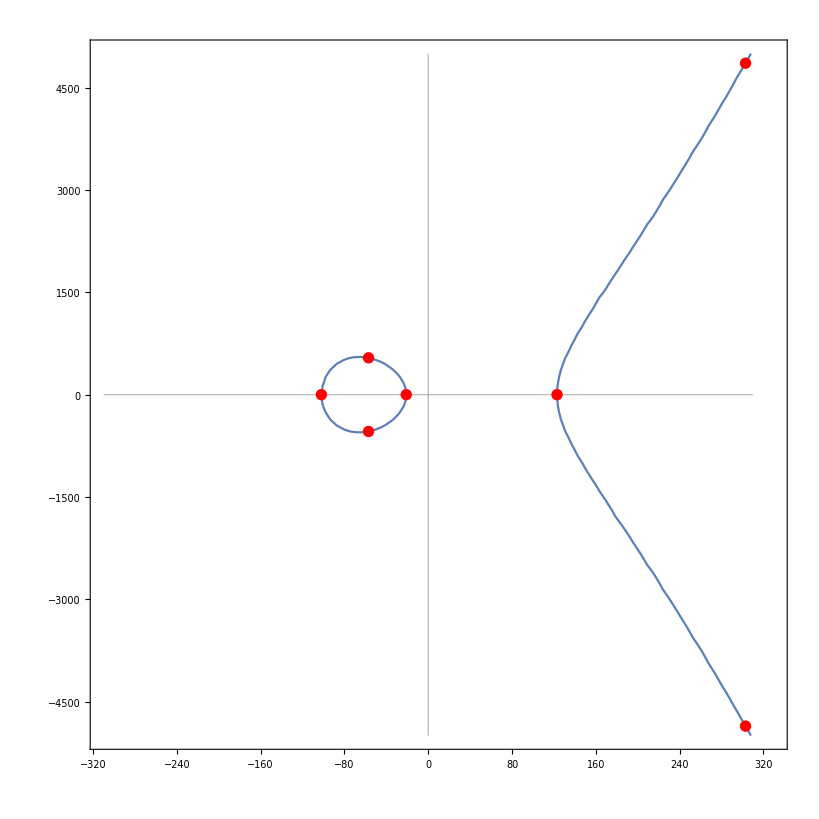

```mathematica
Show[ContourPlot[F[x,y]==0,{x,-310,330},{y,-5000,5000}],
Graphics[{Gray,Opacity[0.5],Line[{{-310,0},{310,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-5000},{0,5000}}]}],
Graphics[{Red,PointSize[.01],Point[G]}]
]
```

Bajo el cambio de coordenadas los puntos racionales de la ecuación simplificada se convierten en los puntos racionales de la ecuación de Weierstrass generalizada:

```mathematica
H=Table[coord[p],{p,G}]
```

{{-13/4,9/8},{-1,0},{3,-2},{8,-27},{8,18},{-2,-2},{-2,3}}

Graficamos los puntos racionales de X_0(15)

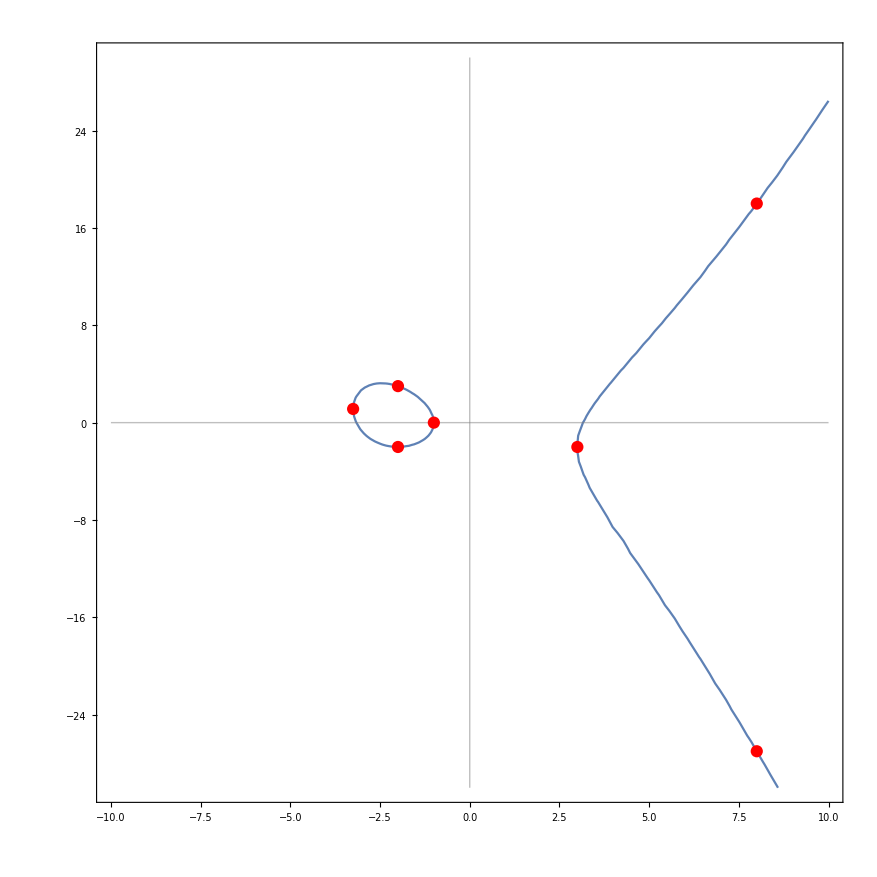

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-10,10},{y,-30,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{Red,PointSize[.01],Point[H]}]]
```

Graficamos las tangentes a cada punto, salvo los puntos de tangente vertical que marcamos en verde:

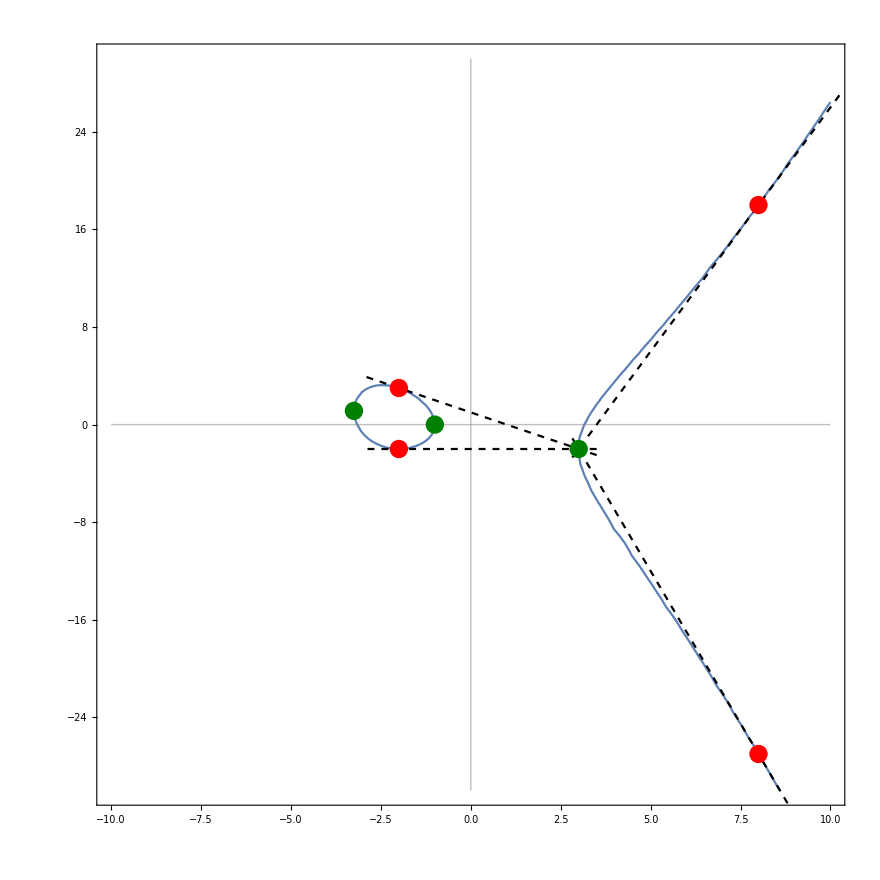

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-10,10},{y,-30,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
ParametricPlot[{Derivative[0,1][f][-2,-2]t,Derivative[1,0][f][-2,-2]t}+{-2,-2},{t,-1.1,0.2},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[1,0][f][-2,3]t,Derivative[0,1][f][-2,3]t}+{-2,3},{t,-1.1,0.2},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[0,1][f][8,18]t,Derivative[1,0][f][8,18]t}+{8,18},{t,-.05,.115},PlotStyle->{Black,Dashed}],
ParametricPlot[{-Derivative[0,1][f][8,-27]t,Derivative[1,0][f][8,-27]t}+{8,-27},{t,-0.115,1},PlotStyle->{Black,Dashed}],
Graphics[{Red,PointSize[.015],Point[{{8,-27},{8,18},{-2,-2},{-2,3}}]}],
Graphics[{green,PointSize[.015],Point[{{-13/4,9/8},{-1,0},{3,-2}}]}]
]
```

Graficamos las dos órbitas de la acción R↦R+P donde  P=(-2,-2) .

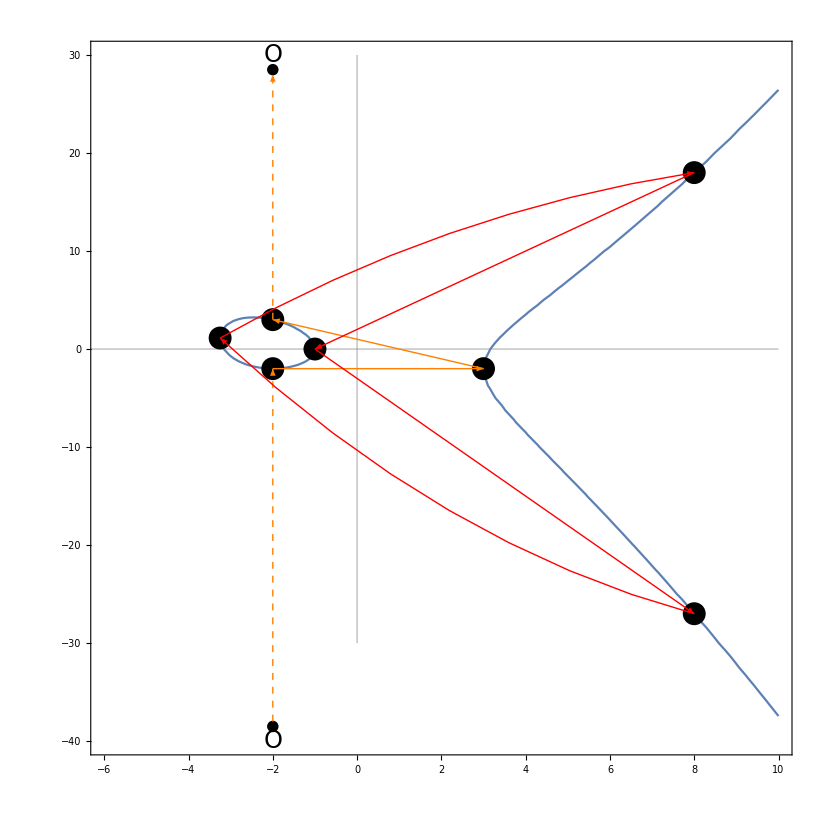

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-6,10},{y,-40,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{PointSize[.01],Inset[Style["O",Italic,Black,24],{-2,30}],Inset[Style["O",Italic,Black,24],{-2,-40}],Point[{{-2,28.5},{-2,-38.5}}]}],
Graphics[{PointSize[.02],Point[H]}],
Graphics[{Arrowheads[.02],Orange,Arrow[{{-2,-2},{3,-2}}]}],
Graphics[{Arrowheads[.02],Orange,Arrow[{{3,-2},{-2,3}}]}],
Graphics[{Arrowheads[.02],Orange,Dashed,Arrow[{{-2,3},{-2,28}}]}],
Graphics[{Arrowheads[.02],Orange,Dashed,Arrow[{{-2,-38},{-2,-2}}]}],
Graphics[{Arrowheads[.02],Red,Arrow[{{8,18},{-1,0}}]}],
Graphics[{Arrowheads[.02],Red,Arrow[{{-1,0},{8,-27}}]}],
Graphics[{Arrowheads[.02],Red,Arrow[BezierCurve[{{8,-27},{2,-20},{-13/4,9/8}}]]}],
Graphics[{Arrowheads[.02],Red,Arrow[BezierCurve[{{-13/4,9/8},{2,14},{8,18}}]]}]
]
```

Graficamos las dos órbitas de la acción R↦R+Q donde  Q=(-1,0) .

```mathematica
green=Darker[Green,0.5];
```

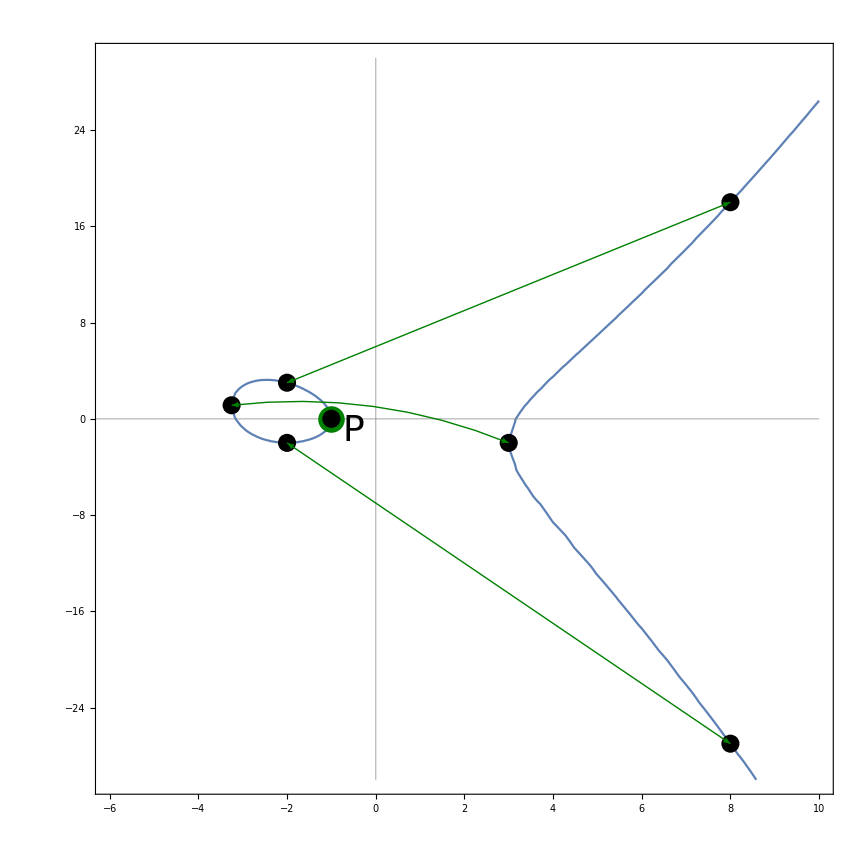

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-6,10},{y,-30,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{PointSize[0.022],Inset[Style["P",Italic,Black,36],{-0.5,-1}],green,Point[{-1,0}]}],
Graphics[{PointSize[.015],Point[H]}],
Graphics[{Arrowheads[{-.03,.03}],green,Thick,Arrow[BezierCurve[{{3,-2},{0,2.5},{-13/4,9/8}}]]}],
Graphics[{Arrowheads[{-.03,.03}],green,Thick,Arrow[{{-2,3},{8,18}}]}],
Graphics[{Arrowheads[{-.03,.03}],green,Thick,Arrow[{{-2,-2},{8,-27}}]}]
]
```

Graficamos las dos órbitas de la acción R↦R+Q donde  Q=(-13/4,9/8) .

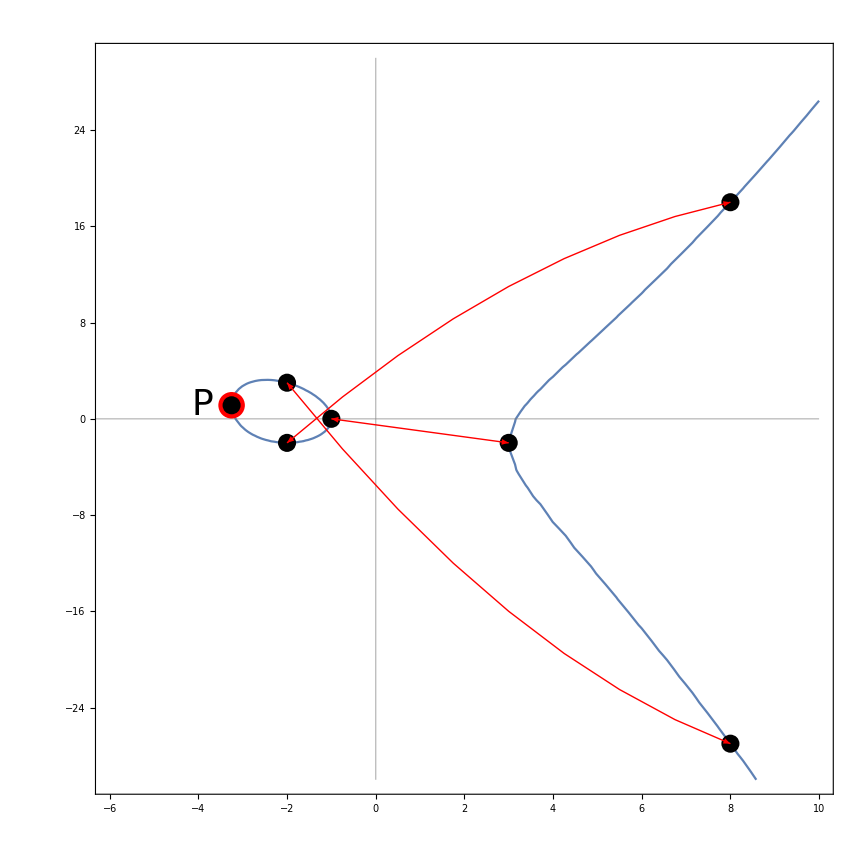

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-6,10},{y,-30,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{PointSize[0.022],Inset[Style["P",Italic,Black,36],{-3.9,9/8}],Red,Point[{-13/4,9/8}]}],
Graphics[{PointSize[.015],Point[H]}],
Graphics[{Arrowheads[{-.03,.03}],Red,Thick,Arrow[{{3,-2},{-1,0}}]}],
Graphics[{Arrowheads[{-.03,.03}],Red,Thick,Arrow[BezierCurve[{{-2,-2},{3,14},{8,18}}]]}],
Graphics[{Arrowheads[{-.03,.03}],Red,Thick,Arrow[BezierCurve[{{8,-27},{3,-20},{-2,3}}]]}]
]
```

Graficamos las dos órbitas de la acción R↦R+Q donde  Q=(3,-2) .

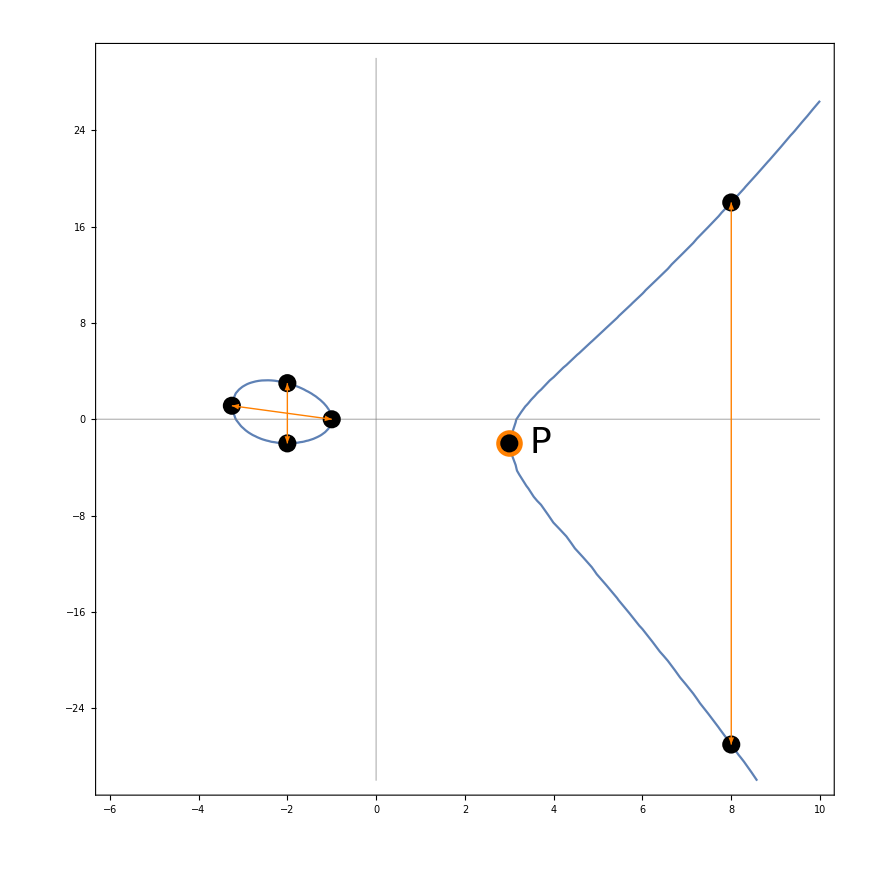

```mathematica
Show[ContourPlot[f[x,y]==0,{x,-6,10},{y,-30,30},AspectRatio->1],
Graphics[{Gray,Opacity[0.5],Line[{{-10,0},{10,0}}]}],
Graphics[{Gray,Opacity[0.5],Line[{{0,-30},{0,30}}]}],
Graphics[{PointSize[0.022],Inset[Style["P",Italic,Black,36],{3.7,-2}],Orange,Point[{3,-2}]}],
Graphics[{PointSize[.015],Point[H]}],
Graphics[{Arrowheads[{-.02,.02}],Orange,Thick,Arrow[{{-13/4,9/8},{-1,0}}]}],
Graphics[{Arrowheads[{-.02,.02}],Orange,Thick,Arrow[{{-2,3},{-2,-2}}]}],
Graphics[{Arrowheads[{-.03,.03}],Orange,Thick,Arrow[{{8,18},{8,-27}}]}]
]
```

```mathematica
63^2-4(-11664)
```

50625

```mathematica
FactorInteger[50625]
```

{{3,4},{5,4}}

```mathematica
15^4
```

50625